# Perron-Frobenius Theorem

Consider a real square matrix with all entries positive. We will verify that it has a unique eigenvalue with the largest magnitude among all its eigenvalues, and this unique eigenvalue is real.

```mathematica
M1={{1, 4, 3}, {1, 5, 6}, {7, 4, 2}};
M1//MatrixForm
```

(1 | 4 | 3
1 | 5 | 6
7 | 4 | 2)

```mathematica
Eigvals=Eigenvalues[M1]//N
```

{11.26,-1.62998+1.43182 ⅈ,-1.62998-1.43182 ⅈ}

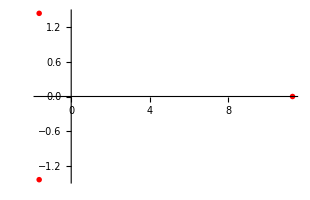

```mathematica
ComplexListPlot[Eigvals, PlotStyle->Red, AspectRatio->Automatic, PlotRange->Full]
```

```mathematica
Abs[Eigvals]//N
```

{11.26,2.16955,2.16955}

Thus, one can see that the theorem holds for this matrix. The largest eigenvalue (decided by magnitude) is unique and real. Note that Mathematica automatically sorts the list of eigenvalues in descending order of their absolute magnitudes.

Let us try the same recipe for another, larger matrix.

```mathematica
M2=RandomReal[{0.01, 10}, {6,6}]; (* Change the order to {n, n} to get an n x n matrix*)
M2//MatrixForm
```

(6.59661 | 5.23809 | 6.5581 | 8.32377 | 1.3222 | 1.94344
1.28643 | 1.90696 | 2.1079 | 8.81889 | 5.35714 | 0.788015
4.40436 | 0.0978618 | 9.06731 | 9.93161 | 4.18403 | 4.65484
4.55768 | 9.32862 | 7.34244 | 4.65226 | 4.90762 | 5.1751
4.89032 | 9.62835 | 7.5474 | 5.94535 | 1.95403 | 6.81071
9.35592 | 4.19087 | 1.90802 | 4.39035 | 0.110376 | 1.32521)

```mathematica
Eigvals=Eigenvalues[M2]//N
```

{29.9996+0. ⅈ,-7.9612+0. ⅈ,4.93764+0. ⅈ,0.596669+4.22987 ⅈ,0.596669-4.22987 ⅈ,-2.66705+0. ⅈ}

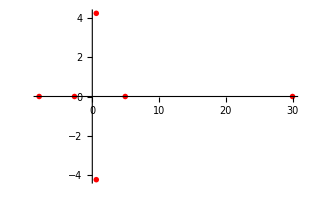

```mathematica
ComplexListPlot[Eigvals, PlotStyle->Red, AspectRatio->Automatic, PlotRange->Full]
```

```mathematica
Abs[Eigvals]//N
```

{29.9996,7.9612,4.93764,4.27174,4.27174,2.66705}

Thus, we have verified the same result for the matrix with real positive entries chosen randomly out of a range.

Now we verify another implication of the theorem - that the eigenvector corresponding to the highest magnitude eigenvalue can be chosen to have all positive components.

```mathematica
Eigvecs=Eigenvectors[M2]
```

{{0.414672+0. ⅈ,0.298602+0. ⅈ,0.467826+0. ⅈ,0.468678+0. ⅈ,0.46895+0. ⅈ,0.283636+0. ⅈ},{-0.11175+0. ⅈ,0.590431+0. ⅈ,0.406692+0. ⅈ,-0.397582+0. ⅈ,-0.560001+0. ⅈ,-0.0428076+0. ⅈ},{0.159816+0. ⅈ,-0.522793+0. ⅈ,0.764959+0. ⅈ,-0.249272+0. ⅈ,-0.210371+0. ⅈ,-0.097937+0. ⅈ},{0.149532+0.362358 ⅈ,-0.243396+0.0847425 ⅈ,-0.327256-0.246916 ⅈ,-0.0713513-0.0159604 ⅈ,0.0921894-0.176492 ⅈ,0.752899+0. ⅈ},{0.149532-0.362358 ⅈ,-0.243396-0.0847425 ⅈ,-0.327256+0.246916 ⅈ,-0.0713513+0.0159604 ⅈ,0.0921894+0.176492 ⅈ,0.752899+0. ⅈ},{0.36361+0. ⅈ,-0.133817+0. ⅈ,0.0796644+0. ⅈ,-0.434756+0. ⅈ,0.754309+0. ⅈ,-0.292471+0. ⅈ}}

The first eigenvector corresponds to the first eigenvalue, which has the largest magnitude.

```mathematica
Eigvecs[[1]]//N//FullSimplify
```

{0.414672+0. ⅈ,0.298602+0. ⅈ,0.467826+0. ⅈ,0.468678+0. ⅈ,0.46895+0. ⅈ,0.283636+0. ⅈ}

Thus, the eigenvector can be chosen to have all positive entries. Note that the sign in front of the entries may be negative, but it is known that any multiple of an eigenvector is also an eigenvector.